```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Get["MergerTransport/Merger2DProton.m"]
```

## 0 spectrum

### algorithm to sort files according to last binnumber

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_1-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_C_da0_a-1050_179-264.txt}

```mathematica
RefSpectrum=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,7}],1];
```

### show single core timing

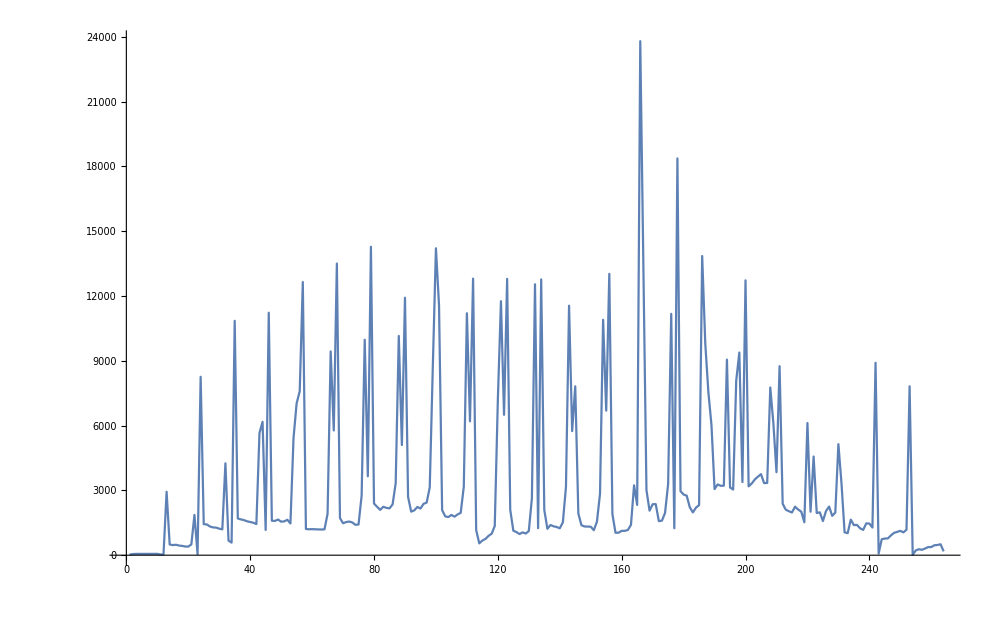

```mathematica
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000]
```

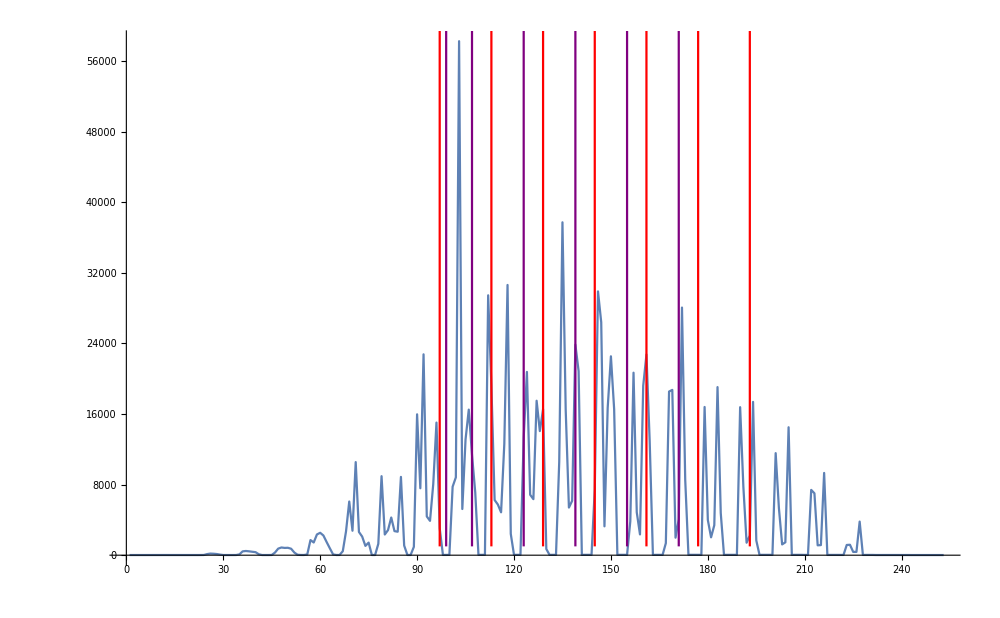

```mathematica
Show[
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000],
ParametricPlot[{{97,1000*d},{113,1000*d},{129,1000*d},{145,1000*d},{161,1000*d},{177,1000*d},{193,1000*d}},{d,1,253},PlotStyle->Red],
ParametricPlot[{{99,1000*d},{107,1000*d},{123,1000*d},{139,1000*d},{155,1000*d},{171,1000*d}},{d,1,253},PlotStyle->Purple]
]
```

## get Bin data

```mathematica
xStart=0.025;
xEnd=0.055;
yStart=-0.02;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
xyBins[[1]]
```

{{0.025,0.02625},{-0.02,-0.015909}}

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto={{-0.06999999999999999,-0.06499999999999999,-0.05999999999999999,-0.05499999999999999,-0.04999999999999999,-0.04499999999999999,-0.039999999999999994,-0.03499999999999999,-0.029999999999999992,-0.024999999999999994,-0.01999999999999999,-0.014999999999999993,-0.009999999999999995,-0.0049999999999999906,1.3877787807814457*^-17,0.0050000000000000044,0.010000000000000009,0.015000000000000013,0.020000000000000004,0.02500000000000001,0.030000000000000013,0.035,0.04000000000000001,0.045},{-1.0540019999999999,-1.049002,-1.0440019999999999,-1.039002,-1.0340019999999999,-1.029002,-1.0240019999999999,-1.019002,-1.0140019999999998,-1.009002,-1.0040019999999998,-0.9990019999999998,-0.9940019999999998,-0.9890019999999999,-0.9840019999999998,-0.9790019999999999,-0.9740019999999999,-0.9690019999999999,-0.9640019999999999,-0.9590019999999999,-0.9540019999999999,-0.9490019999999999,-0.9440019999999999},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=0.999002
```

0.999002

```mathematica
xyBins[[1,1]]
```

{0.025,0.02625}

```mathematica
{Table[(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,{i,Length[xyBins]}],Table[(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,{i,Length[xyBins]}]}
```

{{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375},{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375}}

```mathematica
Clear[BinCenters]
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,(xyBins[[i,2,1]]+xyBins[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
XYBinCentersYHalf[[1]]
```

{0.025625,-0.0179545}

## check spectrum

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

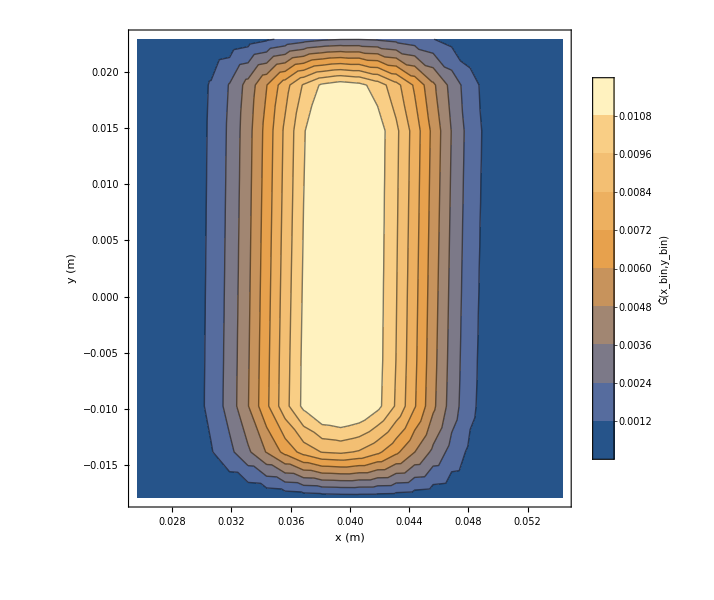

```mathematica
TransferContourPlot=ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/Transfer3D.png",Transfer3DPlot,ImageResolution->450];
Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

# dBRxB, k=-15.13

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b0/"];
```

```mathematica
dBRxBSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_145-160.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_161-176.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_177-192.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_193-253.txt}

```mathematica
dBRxBSpectrumb0=Flatten[Table[Import[dBRxBSubFileNamesb0[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b15/"];
```

```mathematica
dBRxBSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_1-96.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_97-112.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_113-128.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_129-144.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_145-160.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_161-176.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_177-192.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_193-253.txt}

```mathematica
dBRxBSpectrumb15=Flatten[Table[Import[dBRxBSubFileNamesb15[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b7/"];
```

```mathematica
dBRxBSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_145-160.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_161-176.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_177-192.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_193-253.txt}

```mathematica
dBRxBSpectrumb75=Flatten[Table[Import[dBRxBSubFileNamesb75[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b-7/"];
```

```mathematica
dBRxBSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_1-96.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_97-112.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_113-128.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_129-144.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_145-160.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_161-176.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_177-192.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_193-253.txt}

```mathematica
dBRxBSpectrumbm75=Flatten[Table[Import[dBRxBSubFileNamesbm75[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b-15/"];
```

```mathematica
dBRxBSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_145-160.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_161-176.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_177-192.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_193-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dBRxBSpectrumbm15=Flatten[Import[#,"Table"]&/@dBRxBSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,-0.05,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]]}]];
```

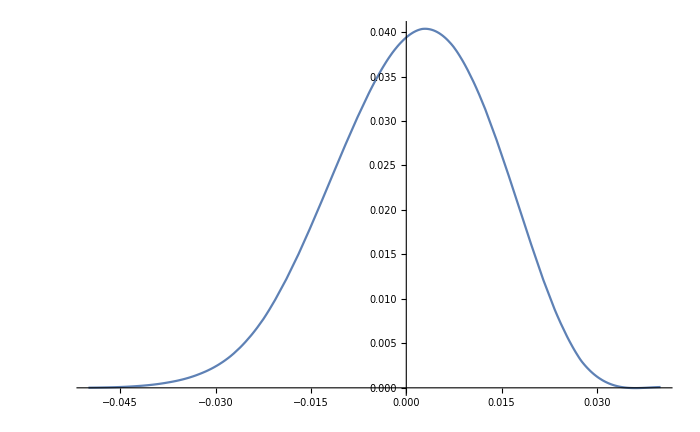

```mathematica
Plot[RefSpectrumInter[x,0.],{x,-0.05,0.04},PlotRange->All]
```

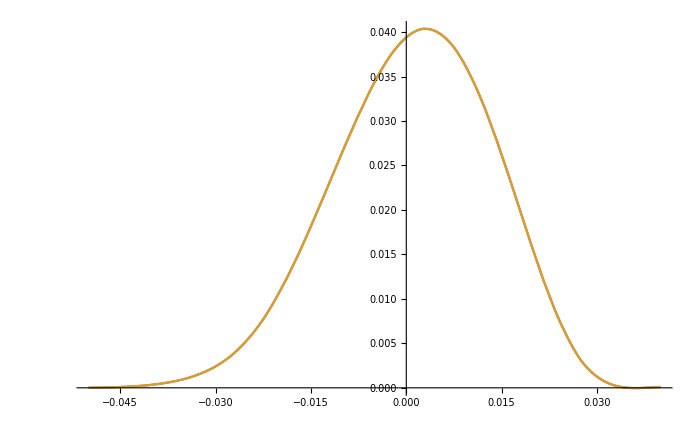

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,-0.05,0.04},PlotRange->All]
```

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm75[[All,2]]/Total[dBRxBSpectrumbm75[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb15[[All,2]]/Total[dBRxBSpectrumb15[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}]];
```

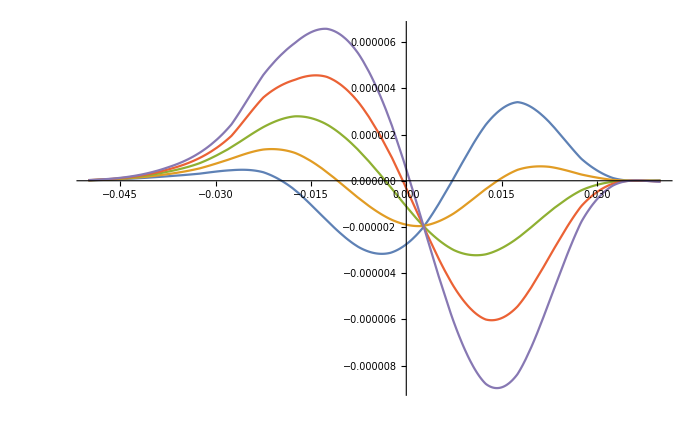

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,-0.05,0.04},PlotRange->All]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

```mathematica
dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.36863×10^-10,4.07996×10^-10,3.19292×10^-11,1.42553×10^-13,0.,0.,0.,0.,0.,0.,2.59993×10^-9,1.4643×10^-7,3.11107×10^-7,2.31112×10^-7,1.36065×10^-7,4.76193×10^-8,1.2291×10^-9,0.,0.,0.,0.,2.03998×10^-7,3.11947×10^-6,6.84058×10^-6,6.62686×10^-6,4.83431×10^-6,1.93743×10^-6,1.46401×10^-7,0.,0.,0.,7.05888×10^-10,3.16048×10^-6,0.0000234196,0.0000493116,0.0000531614,0.0000408369,0.0000188314,2.86494×10^-6,9.03721×10^-9,0.,0.,3.23234×10^-7,0.0000177044,0.000100397,0.000205907,0.000234623,0.000186966,0.0000927304,0.0000185237,5.51569×10^-7,0.,0.,9.71469×10^-7,0.0000595062,0.000309378,0.000628561,0.000736105,0.000600097,0.000310256,0.0000712827,3.0292×10^-6,0.,0.,2.74528×10^-6,0.000152579,0.000774239,0.00159952,0.0018878,0.00156135,0.000823198,0.000199853,9.54737×10^-6,0.,0.,3.88467×10^-6,0.000313669,0.00168782,0.00369996,0.00433486,0.00363987,0.00190851,0.000449662,0.0000222802,0.,0.,0.,0.000531094,0.00323004,0.00773746,0.00898466,0.00770991,0.00398244,0.000844609,0.0000358352,0.,0.,0.,0.000740222,0.00535976,0.0139127,0.0161335,0.0141924,0.0072312,0.00135022,0.0000226273,0.,0.,0.,0.000863278,0.00775098,0.0214202,0.0249538,0.0223604,0.0112936,0.00185325,7.06033×10^-7,0.,0.,0.,0.000809817,0.00986941,0.0288684,0.0337018,0.0306964,0.0153352,0.00211014,0.,0.,0.,0.,0.00054451,0.0110646,0.0345881,0.0402363,0.0373612,0.0183953,0.00197547,0.,0.,0.,0.,0.000206637,0.0108394,0.0369185,0.0424076,0.0403525,0.0194847,0.00143803,0.,0.,0.,0.,0.0000203655,0.00914436,0.0348098,0.0391745,0.0382876,0.0180841,0.000732696,0.,0.,0.,0.,0.,0.00645827,0.0283774,0.0311792,0.0311918,0.014377,0.000241551,0.,0.,0.,0.,0.,0.00375251,0.019043,0.0204596,0.0208311,0.00937791,0.000013516,0.,0.,0.,0.,0.,0.00163446,0.00951662,0.0100221,0.0102987,0.00457549,0.,0.,0.,0.,0.,0.,0.000440399,0.00285973,0.00296835,0.00305719,0.00136139,0.,0.,0.,0.,0.,0.,0.0000450576,0.000308296,0.000317597,0.000327138,0.000146399,0.,0.,0.,0.,0.,0.,4.85721×10^-8,3.66074×10^-7,3.75038×10^-7,3.84282×10^-7,6.12352×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
BRxBDataList={dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]],dBRxBSpectrumbm75[[All,2]]/Total[dBRxBSpectrumbm75[[All,2]]],dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]],dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]],dBRxBSpectrumb15[[All,2]]/Total[dBRxBSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

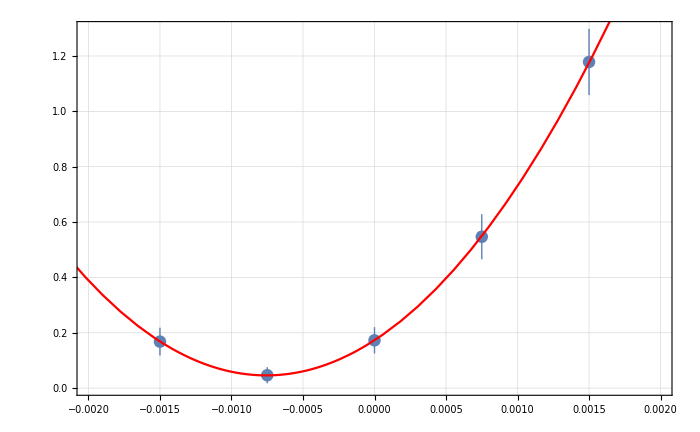
{{{1.67947×10^-10,4.64371×10^-11,1.7259×10^-10,5.46827×10^-10,1.17847×10^-9},{5.02571×10^-11,2.93313×10^-11,4.7551×10^-11,8.1608×10^-11,1.19841×10^-10}},b0 =  | -0.000756452
FittedModel[4.59438×10^-11+0.000221834 (0.000756452+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000756452 | 0.0000982889 | -7.6962 | 0.016467
scale | 0.000221834 | 0.0000303947 | 7.29843 | 0.0182607
yoffset | 4.59438×10^-11 | 2.41516×10^-11 | 1.90231 | 0.197472 | 
 | DF | SS | MS
Model | 3 | 168.444 | 56.1481
Error | 2 | 0.00208928 | 0.00104464
Uncorrected Total | 5 | 168.447 | 
Corrected Total | 4 | 109.764 |  | ,-Graphics-}

```mathematica
BRxBInvest=TransferToRefParableFit[RefSpectrum[[All,2]],BRxBDataList,bList, 4]
```

```mathematica
BRxBInvest[[2,1,1,2]]/(5*10^-5)
```

-15.129